# Vaje za 3. teden

6.  3.  2025

## Naloga 0

Napiši  funkcijo quickSort, ki sprejme seznam in vrne urejen seznam. Za urejanje naj uporabi algoritem quick sort

```mathematica
quickSort[seznam_]:=
If[Length[seznam]<= 1, seznam,
Module[{seznamMan, seznamEna, seznamVec},
seznamMan = Select[seznam, # < First[seznam]&];
seznamEna = Select[seznam, # == First[seznam] &];
seznamVec = Select[seznam, # > First[seznam] &];
Join[quickSort[seznamMan], seznamEna,  quickSort[seznamVec]]
]]
```

```mathematica
quickSort[{2, 4, 1, 7, 6, 5, 3, 9, 10}];
sez = Table[RandomInteger[100], {i, 100}];
quickSort[sez]
```

quickSort[{26,13,45,74,33,74,45,99,46,100,26,25,6,20,70,6,68,13,49,60,75,98,38,94,16,43,19,44,83,73,41,38,27,8,64,92,81,98,23,28,80,50,61,50,19,59,12,17,50,33,55,21,73,86,48,74,51,30,38,82,88,46,23,56,79,62,88,7,51,14,53,8,87,70,18,33,32,99,83,14,7,91,73,73,45,40,61,4,67,54,25,38,61,33,51,63,54,25,77,18}]

## Naloga 1

Napišite prepisovalno pravilo, ki bo izračunalo produkt dvečlenika z dvočlenikom. S tem pravilom oenostavi izraz (2x - 4)(3 - 4y).

```mathematica
izraz = {a_*(b_ + c_):> a * b + a * c};
(2x - 4)(3 - 4y)//.izraz
```

-12+6 x+16 y-8 x y

## Naloga 2

a) Definiraj funkcijo nakljucnaStevila, ki sprejme naravno število n in vrne seznam naključnih celih števil med -100 in 100 dolžine n.
c) S  pomočjo  prepisovalnih  pravil implementiraj urejanje z mehurčki (Bubble sort).

```mathematica
nakljucnaStevila[n_] := Table[RandomInteger[{-100, 100}], {i, 1, n}];
randints = nakljucnaStevila[10]
```

{-87,-42,-61,-69,-34,77,91,0,11,-54}

```mathematica
prepZamenjaj = {a___, b_, c_, d___} /; b > c :> {a, c, b, d};
randints //. prepZamenjaj
```

{-87,-69,-61,-54,-42,-34,0,11,77,91}

## Naloga 3

- Definiraj funkcijo ZadnjaStevka, ki kot argument sprejme naravno število n in vrne zadnjo števko števila n. (ZadnjaStevka(8138719) vrne 9)
- Definiraj funkcijo PrvaStevka, ki kot argument sprejme naravno število n in vrne prvo števko števila n. (PrvaStevka(8138719) vrne 8)
- Definiraj funkcijo Parabola, ki sprejme koeficiente parabole a, b in c in nariše graf parabole ax^2 + bx + c. Graf naj bo narisan tako, da bo teme parabole vedno vidno na sliki.

9

8

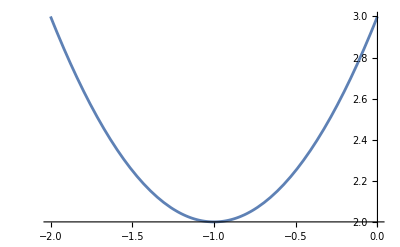

```mathematica
ZadnjaStevka[n_Integer]:= Mod[n, 10];
PrvaStevka[n_Integer]:= Floor[Abs[n]/ 10^Floor[Log10[Abs[n]]]];
Parabola[a_,b_,c_]:= 
Plot[a x^2 + b x + c, {x, -b/(2a) - 1, -b/(2a) + 1}]
ZadnjaStevka[8138719]
PrvaStevka[8138719]
Parabola[1,2,3]
```

## Naloga 4

Definiraj naslednje sezname:
- {1/(2^20), 1/(2^19), ..., 1/2, 1, 2, 4, 8, ..., 2^24}
- {{}, {1}, {2}, {3}, ..., {99}, {99}, {98}, ..., {2}, {1}, {}}
- seznam dolžine 100, v katerem je vsak naslednji element za eno mesto bolj natančen približek števila π. ({3, 3.1, 3.14, ...})

```mathematica
f[n_]:= 2^n;
Table[f[i], {i, -20, 24}]
```

{1/1048576,1/524288,1/262144,1/131072,1/65536,1/32768,1/16384,1/8192,1/4096,1/2048,1/1024,1/512,1/256,1/128,1/64,1/32,1/16,1/8,1/4,1/2,1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768,65536,131072,262144,524288,1048576,2097152,4194304,8388608,16777216}

```mathematica
f[n_] := Piecewise[{{{}, n==0}, {{n}, n != 0}}];
tmp = Table[f[i], {i, 0, 99}];
Join[tmp, Reverse[tmp]]
```

{{},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},{52},{53},{54},{55},{56},{57},{58},{59},{60},{61},{62},{63},{64},{65},{66},{67},{68},{69},{70},{71},{72},{73},{74},{75},{76},{77},{78},{79},{80},{81},{82},{83},{84},{85},{86},{87},{88},{89},{90},{91},{92},{93},{94},{95},{96},{97},{98},{99},{99},{98},{97},{96},{95},{94},{93},{92},{91},{90},{89},{88},{87},{86},{85},{84},{83},{82},{81},{80},{79},{78},{77},{76},{75},{74},{73},{72},{71},{70},{69},{68},{67},{66},{65},{64},{63},{62},{61},{60},{59},{58},{57},{56},{55},{54},{53},{52},{51},{50},{49},{48},{47},{46},{45},{44},{43},{42},{41},{40},{39},{38},{37},{36},{35},{34},{33},{32},{31},{30},{29},{28},{27},{26},{25},{24},{23},{22},{21},{20},{19},{18},{17},{16},{15},{14},{13},{12},{11},{10},{9},{8},{7},{6},{5},{4},{3},{2},{1},{}}

```mathematica
f[n_] := N[π, n]
Table[f[i], {i, 1, 100}]
```

{3.,3.1,3.14,3.142,3.1416,3.14159,3.141593,3.1415927,3.14159265,3.141592654,3.1415926536,3.14159265359,3.14159265359,3.1415926535898,3.14159265358979,3.141592653589793,3.1415926535897932,3.14159265358979324,3.141592653589793238,3.1415926535897932385,3.14159265358979323846,3.141592653589793238463,3.1415926535897932384626,3.14159265358979323846264,3.141592653589793238462643,3.1415926535897932384626434,3.14159265358979323846264338,3.141592653589793238462643383,3.1415926535897932384626433833,3.14159265358979323846264338328,3.14159265358979323846264338328,3.1415926535897932384626433832795,3.1415926535897932384626433832795,3.141592653589793238462643383279503,3.1415926535897932384626433832795029,3.14159265358979323846264338327950288,3.141592653589793238462643383279502884,3.1415926535897932384626433832795028842,3.1415926535897932384626433832795028842,3.141592653589793238462643383279502884197,3.1415926535897932384626433832795028841972,3.14159265358979323846264338327950288419717,3.141592653589793238462643383279502884197169,3.1415926535897932384626433832795028841971694,3.1415926535897932384626433832795028841971694,3.141592653589793238462643383279502884197169399,3.1415926535897932384626433832795028841971693994,3.14159265358979323846264338327950288419716939938,3.141592653589793238462643383279502884197169399375,3.1415926535897932384626433832795028841971693993751,3.14159265358979323846264338327950288419716939937511,3.141592653589793238462643383279502884197169399375106,3.1415926535897932384626433832795028841971693993751058,3.14159265358979323846264338327950288419716939937510582,3.141592653589793238462643383279502884197169399375105821,3.141592653589793238462643383279502884197169399375105821,3.14159265358979323846264338327950288419716939937510582097,3.141592653589793238462643383279502884197169399375105820975,3.1415926535897932384626433832795028841971693993751058209749,3.14159265358979323846264338327950288419716939937510582097494,3.141592653589793238462643383279502884197169399375105820974945,3.1415926535897932384626433832795028841971693993751058209749446,3.14159265358979323846264338327950288419716939937510582097494459,3.141592653589793238462643383279502884197169399375105820974944592,3.1415926535897932384626433832795028841971693993751058209749445923,3.14159265358979323846264338327950288419716939937510582097494459231,3.141592653589793238462643383279502884197169399375105820974944592308,3.1415926535897932384626433832795028841971693993751058209749445923078,3.14159265358979323846264338327950288419716939937510582097494459230782,3.141592653589793238462643383279502884197169399375105820974944592307816,3.1415926535897932384626433832795028841971693993751058209749445923078164,3.14159265358979323846264338327950288419716939937510582097494459230781641,3.141592653589793238462643383279502884197169399375105820974944592307816406,3.1415926535897932384626433832795028841971693993751058209749445923078164063,3.14159265358979323846264338327950288419716939937510582097494459230781640629,3.141592653589793238462643383279502884197169399375105820974944592307816406286,3.1415926535897932384626433832795028841971693993751058209749445923078164062862,3.14159265358979323846264338327950288419716939937510582097494459230781640628621,3.141592653589793238462643383279502884197169399375105820974944592307816406286209,3.141592653589793238462643383279502884197169399375105820974944592307816406286209,3.141592653589793238462643383279502884197169399375105820974944592307816406286209,3.141592653589793238462643383279502884197169399375105820974944592307816406286208999,3.1415926535897932384626433832795028841971693993751058209749445923078164062862089986,3.14159265358979323846264338327950288419716939937510582097494459230781640628620899863,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628,3.14159265358979323846264338327950288419716939937510582097494459230781640628620899862803,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628035,3.1415926535897932384626433832795028841971693993751058209749445923078164062862089986280348,3.14159265358979323846264338327950288419716939937510582097494459230781640628620899862803483,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825,3.1415926535897932384626433832795028841971693993751058209749445923078164062862089986280348253,3.14159265358979323846264338327950288419716939937510582097494459230781640628620899862803482534,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342,3.1415926535897932384626433832795028841971693993751058209749445923078164062862089986280348253421,3.14159265358979323846264338327950288419716939937510582097494459230781640628620899862803482534212,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117,3.1415926535897932384626433832795028841971693993751058209749445923078164062862089986280348253421171,3.14159265358979323846264338327950288419716939937510582097494459230781640628620899862803482534211707,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068}

## Naloga 5

Definiraj funkcijo, ki je za pozitivne x enaka sin(x)/x, za x manjši ali enak 0 pa je enaka cos(x). Pomagaj si s funkcijo `Piecewise`.

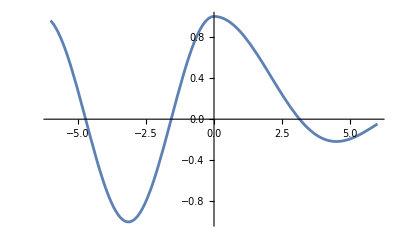

```mathematica
f[x_]:= Piecewise[{{Sin[x]/x, x>0}, {Cos[x], x <= 0}}]
Plot[f[x], {x, -6, 6}]
```

```mathematica
Ž
```

## Naloga 6

Dano je zaporedje  
a) V Mathematici definiraj zaporedje .
b) Definiraj seznam, ki vrne prvih 30 členov zaporedja.
c) Izračunaj limito zaporedja . Izračunaj tudi limito zaporedja . Ali vrsta  konvergira?
d) Izračunaj numerični približek vsote vrste  (uporabi NSum).

```mathematica
Clear[a, n]
a[n_]:= ((2n^2 + n + 1)/(2n^2-1))^(-n^2)
prvih30 = Table[a[i], {i, 1 ,30}]
N /@ prvih30
```

{0.25,0.163992,0.0982282,0.0589603,0.0354978,0.0214154,0.0129368,0.00782207,0.00473251,0.00286459,0.00173453,0.00105055,0.000636419,0.000385603,0.000233666,0.000141611,0.0000858304,0.0000520256,0.000031537,0.0000191183,0.0000115904,7.02691×10^-6,4.26037×10^-6,2.58312×10^-6,1.56622×10^-6,9.49668×10^-7,5.75839×10^-7,3.49172×10^-7,2.11731×10^-7,1.28392×10^-7}

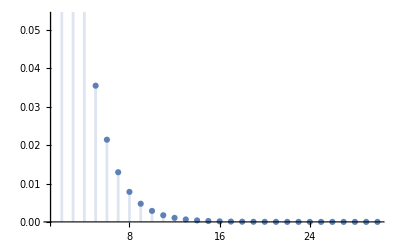

```mathematica
ListPlot[prvih30];
DiscretePlot[a[n], {n, 1, 30}]
```

```mathematica
DiscreteLimit[a[n], n -> Infinity]
DiscreteLimit[Power[a[n], 1/n], n -> Infinity]
```

0

1/(√ⅇ)

```mathematica
s[n_] := NSum[a[m], {m, n}]
s[Infinity]
```

0.660849

## Naloga 7

Dano  je  rekurzivno  zaporedje .

a) V Mathematici definiraj zaporedje  z začetnim členom .
b) Izračunaj prvih 5 členova zaporedja . Nato vse vse izraze razširi in združi na skupni ulomek.

```mathematica
ClearAll[b]
a[1] := b
a[n_] := 1/6 * (a[n - 1]^2 + a[n - 1] + 6) ;
prvihPet = Table[a[i], {i, 1, 5}]
```

{b,1/6 (6+b+b^2),1/6 (6+1/6 (6+b+b^2)+1/36 (6+b+b^2)^2),1/6 (6+1/6 (6+1/6 (6+b+b^2)+1/36 (6+b+b^2)^2)+1/36 (6+1/6 (6+b+b^2)+1/36 (6+b+b^2)^2)^2),1/6 (6+1/6 (6+1/6 (6+1/6 (6+b+b^2)+1/36 (6+b+b^2)^2)+1/36 (6+1/6 (6+b+b^2)+1/36 (6+b+b^2)^2)^2)+1/36 (6+1/6 (6+1/6 (6+b+b^2)+1/36 (6+b+b^2)^2)+1/36 (6+1/6 (6+b+b^2)+1/36 (6+b+b^2)^2)^2)^2)}

```mathematica
Together /@ (Expand /@ prvihPet)
```

{b,1/6 (6+b+b^2),1/216 (288+18 b+19 b^2+2 b^3+b^4),(425088+14256 b+15372 b^2+2268 b^3+1225 b^4+112 b^5+42 b^6+4 b^7+b^8)/279936,1/470184984576(769882226688+16110876672 b+17575315200 b^2+3001380480 b^3+1685350800 b^4+231227136 b^5+93463272 b^6+14717880 b^7+4544065 b^8+616400 b^9+164332 b^10+23744 b^11+5110 b^12+560 b^13+100 b^14+8 b^15+b^16)}

## Naloga 8

Za zaporedje  z začetnima členoma  in  izračunajte njegovo limito. Uporabite RSolveValue.

## Naloga 9

Naslednje naloge reši s pomočjo vnosa z naravnim jezikom (brez znanja sintakse Mathematice in brez pomožnih računov). V vseh primerih se prepričaj, da je Mathematica razumela tvoj ukaz. Glej spodnji primer.

### Primer

Izračunaj 20. števko v decimalnem zapisu števila 1+1/2+1/3+...+1/100.

WolframAlphaQueryResults

### Naloge

Določi 443. števko v decimalnem zapisu števila pi.

Izračunaj ploščino območja med krivuljama f(x)=3x^2+2x+1 in g(x)=4-4x^4.

Izračunaj f(3), kjer je f(x)=1+1/x.

Izračunaj obseg elipse s polosema 4 in 3. Ugotovi približno vrednost.

Matej ima 512 jabolk, Jana pa 1024 jabolk. Koliko jabolk imata Matej in Jana skupaj?

Ali je 1009 praštevilo? Izračunaj vsoto 1/2+1/3+1/5+1/7+1/11+...+1/1009. Kaj predstavlja ta vsota?

## Naloga 10

Naslednje naloge reši z vnosom z naravnim jezikom.

### Naloge

Določi površino Slovenije in skupno dolžno njene meje.

Koliko Slovenij prekrije površino Rusije?

Kolikšna je temperatura sonca?